```mathematica
L=1.1;
h=1;
```

```mathematica
texact[x_,y_]:={{Cos[2 π(x + 1.23 y)],Cos[4 π(x - y)]},{Sin[3 π (x+y/2)],Cos[2 π(x+y^2)]/(1+x)}}
```

```mathematica
t = Import ["/Users/michelecastellana/Desktop/t_sub_mesh.csv"]
```

```mathematica
t11=Table[{t[[i,10]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.,0.12533},{0.057895,-0.23586},{0.11579,-0.56619},{0.17368,-0.82241},{0.23158,-0.971},{0.28947,-0.99253},{0.34737,-0.88415},{0.40526,-0.66006},{0.46316,-0.3496},{0.52105,0.0066178},{0.57895,0.36196},{0.63684,0.66994},{0.69474,0.89025},{0.75263,0.99405},{0.81053,0.96776},{0.86842,0.81481},{0.92632,0.55523},{0.98421,0.22299},{1.0421,-0.13844},{1.1,-0.48175}}

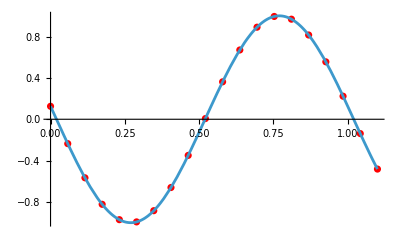

```mathematica
Show[ListPlot[t11,PlotStyle->Red],Plot[texact[x,h][[1,1]],{x,0,L}]]
```

```mathematica
t12=Table[{t[[i,10]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.,1.},{0.057895,0.74672},{0.11579,0.11523},{0.17368,-0.57435},{0.23158,-0.97326},{0.28947,-0.87985},{0.34737,-0.34034},{0.40526,0.37157},{0.46316,0.89478},{0.52105,0.96523},{0.57895,0.54707},{0.63684,-0.14809},{0.69474,-0.76838},{0.75263,-0.99945},{0.81053,-0.72434},{0.86842,-0.082439},{0.92632,0.60105},{0.98421,0.98047},{1.0421,0.86331},{1.1,0.30902}}

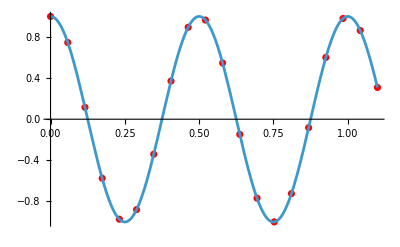

```mathematica
Show[ListPlot[t12,PlotStyle->Red],Plot[texact[x,h][[1,2]],{x,0,L}]]
```

```mathematica
t21=Table[{t[[i,10]],t[[i,4]]},{i,2,Length[t]}]
```

{{0.,-1.},{0.057895,-0.85477},{0.11579,-0.46129},{0.17368,0.066099},{0.23158,0.5743},{0.28947,0.91577},{0.34737,0.99127},{0.40526,0.77886},{0.46316,0.34025},{0.52105,-0.19715},{0.57895,-0.67727},{0.63684,-0.96074},{0.69474,-0.96527},{0.75263,-0.68934},{0.81053,-0.21322},{0.86842,0.32473},{0.92632,0.76839},{0.98421,0.98896},{1.0421,0.9223},{1.1,0.58779}}

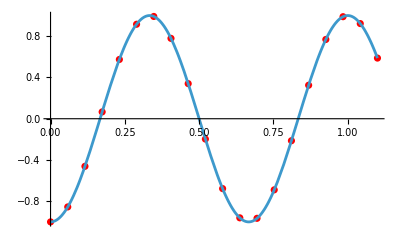

```mathematica
Show[ListPlot[t21,PlotStyle->Red],Plot[texact[x,h][[2,1]],{x,0,L}]]
```

```mathematica
t22=Table[{t[[i,10]],t[[i,5]]},{i,2,Length[t]}]
```

{{0.,1.},{0.057895,0.88342},{0.11579,0.66931},{0.17368,0.39307},{0.23158,0.093773},{0.28947,-0.19037},{0.34737,-0.42626},{0.40526,-0.58922},{0.46316,-0.66522},{0.52105,-0.6517},{0.57895,-0.557},{0.63684,-0.39869},{0.69474,-0.2008},{0.75263,0.0094345},{0.81053,0.20503},{0.86842,0.36249},{0.92632,0.46448},{0.98421,0.5015},{1.0421,0.47265},{1.1,0.38525}}

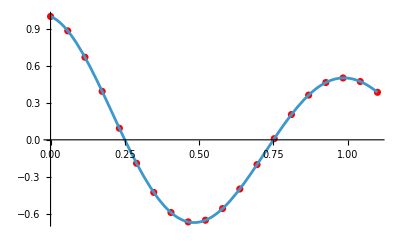

```mathematica
Show[ListPlot[t22,PlotStyle->Red],Plot[texact[x,h][[2,2]],{x,0,L}]]
```